```mathematica
filenames={
"Table_TwoHerbicides_Deterministic_control2_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Deterministic_control3_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Deterministic_control4_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Deterministic_control5_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Deterministic_HighEfficiency_control4_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Deterministic_HighEfficiency_control5_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_Equilibrium_tillage0.txt"
};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../Data/"<>filenames⟦i⟧,"CSV"],{i,Length[filenames]}];
```

## Plot

```mathematica
pos=Position[data⟦7⟧⟦All,{1,2}⟧,{0.3,0.5}]⟦1,1⟧;
```

```mathematica
rallelefraction=Table[PrependTo[data⟦i⟧⟦2;;,15⟧,data⟦7⟧⟦pos,3⟧],{i,1,Length[filenames]-1,1}]
```

{{4.2029×10^-8,2.46514×10^-6,0.000571858,0.092986,0.907574,0.982711,0.993189,0.996566,0.998132,0.99896,0.999416,0.999671,0.999815,0.999896,0.999941,0.999967,0.999981,0.999989,0.999994,0.999997,0.999998,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.},{4.2029×10^-8,4.42769×10^-6,0.00124675,0.194514,0.939124,0.98478,0.993768,0.996821,0.998264,0.999032,0.999457,0.999694,0.999827,0.999903,0.999945,0.999969,0.999983,0.99999,0.999994,0.999997,0.999998,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.},{4.2029×10^-8,2.41891×10^-6,0.000494714,0.0248786,0.479314,0.945022,0.988007,0.996192,0.999011,0.999758,0.999907,0.999955,0.999976,0.999987,0.999993,0.999996,0.999998,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{4.2029×10^-8,4.40016×10^-6,0.00109112,0.0449338,0.61329,0.959344,0.990009,0.996834,0.999195,0.999798,0.99992,0.999961,0.999979,0.999989,0.999994,0.999996,0.999998,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{4.2029×10^-8,2.26259×10^-6,0.000216824,0.00162355,0.0472813,0.919838,0.992853,0.998007,0.999365,0.999786,0.999906,0.999951,0.999973,0.999985,0.999992,0.999995,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{4.2029×10^-8,4.2394×10^-6,0.000480124,0.00156487,0.0885036,0.948147,0.993595,0.998172,0.999415,0.999803,0.999911,0.999954,0.999974,0.999986,0.999992,0.999995,0.999997,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}



```mathematica
ListPlot[rallelefraction⟦All,1;;11⟧,Joined->True,PlotRange->{{-1,10.8},{-0.1,1.1}},Frame->True,DataRange->{0,10},PlotMarkers->{{-Graphics-,0.025},{-Graphics-,0.025},{-Graphics-,0.025},{-Graphics-,0.025},{-Graphics-,0.025},{-Graphics-,0.025}},PlotStyle->{Lighter[Gray],Directive[Dashed,Lighter[Gray]],Lighter[Black],Directive[Dashed,Lighter[Black]],Black,Directive[Dashed,Black]},AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.0015]]]
```

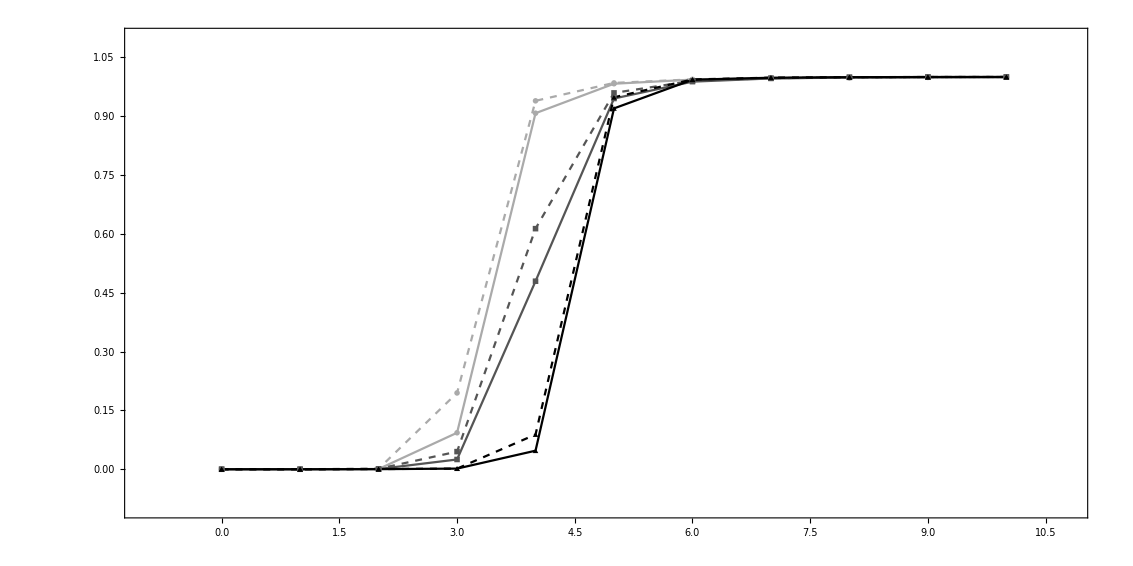

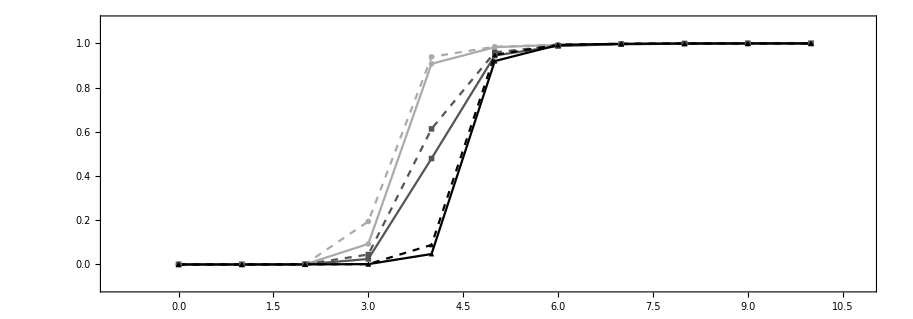

```mathematica
ListPlot[rallelefraction⟦All,1;;11⟧,Joined->True,PlotRange->{{-1,10.8},{-0.1,1.1}},Frame->True,DataRange->{0,10},PlotMarkers->{{-Graphics-,0.03},{-Graphics-,0.03},{-Graphics-,0.03},{-Graphics-,0.03},{-Graphics-,0.03},{-Graphics-,0.03}},PlotStyle->{Lighter[Gray],Directive[Dashed,Lighter[Gray]],Lighter[Black],Directive[Dashed,Lighter[Black]],Black,Directive[Dashed,Black]},AspectRatio->0.35,FrameStyle->Directive[Black,Thickness[0.0015]]]
```